```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

```mathematica
QuantumState["000"]//TraditionalForm
```

000

```mathematica
QuantumOperator["X"]//TraditionalForm
QuantumOperator["Z"]//TraditionalForm
QuantumOperator["CNOT"]//TraditionalForm
QuantumOperator["H"]//TraditionalForm
```

01+10

00-11

0000+0101+1011+1110

1/(√2)00+1/(√2)01+1/(√2)10-1/(√2)11

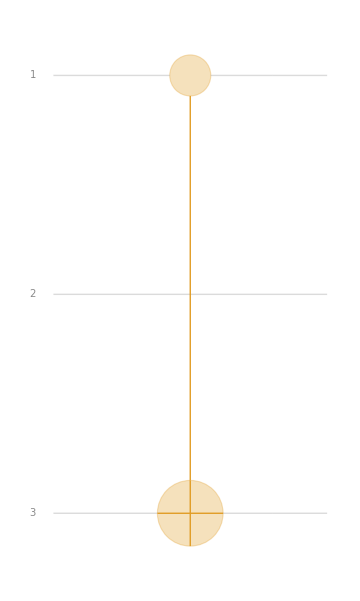

```mathematica
QuantumOperator[{"CNOT"->{1,3}}]["CircuitDiagram"]
```

```mathematica
QuantumOperator["CNOT"]
```

QuantumCircuitOperator[…]

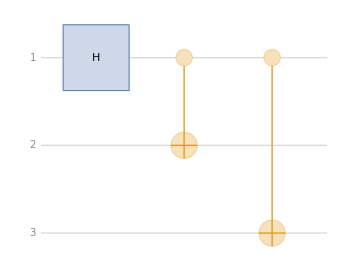

1/(√2)00+1/(√2)01+1/(√2)10-1/(√2)11

0000+0101+1011+1110

0000+0101+1011+1110

1/(√2)000+1/(√2)111

```mathematica
qc=QuantumCircuitOperator[List[
	QuantumOperator["H",{1}],
	QuantumOperator["CNOT"->{1,2}],
	QuantumOperator["CNOT"->{1,3}]
]]
qc["Diagram"]
QuantumOperator["H",{1}]//TraditionalForm
QuantumOperator["CNOT"->{1,2}]//TraditionalForm
QuantumOperator["CNOT"->{1,3}]//TraditionalForm
qc[QuantumState["000"]]//TraditionalForm
```

```mathematica
qc["Diagram"]
```

```mathematica
qc=QuantumCircuitOperator[List[
	QuantumOperator["H",{1}]
]]
qc[QuantumState["000"]]//TraditionalForm
```

QuantumCircuitOperator[…]

1/(√2)000+1/(√2)100

## Second hmk of QC

QuantumCircuitOperator[…]

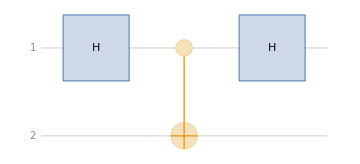

1/(√2)00+1/(√2)01+1/(√2)10-1/(√2)11

0000+0101+1011+1110

0000+0101+1011+1110

(a/(√2)+b/(√2))/(√2)00+(a/(√2)-b/(√2))/(√2)01+(a/(√2)+b/(√2))/(√2)10-(a/(√2)-b/(√2))/(√2)11

```mathematica
qc=QuantumCircuitOperator[List[
	QuantumOperator["H",{1}],
	QuantumOperator["CNOT"->{1,2}],
	QuantumOperator["H"->{1}]
]]
qc["Diagram"]
QuantumOperator["H",{1}]//TraditionalForm
QuantumOperator["CNOT"->{1,2}]//TraditionalForm
QuantumOperator["CNOT"->{1,3}]//TraditionalForm
qc[(a QuantumState["00"] + b QuantumState["10"])]//TraditionalForm
```

```mathematica
(a QuantumState["00"] + b QuantumState["10"])//TraditionalForm
```

a00+b10

0000

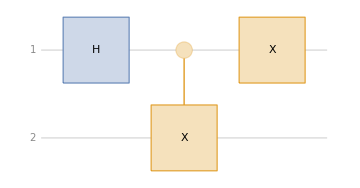

1/(√2)0100+1/(√2)1000

```mathematica
qs=(QuantumState["0000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["H",{1}],
	QuantumOperator["CX",{1,2}],
	QuantumOperator["X",{1}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

0000

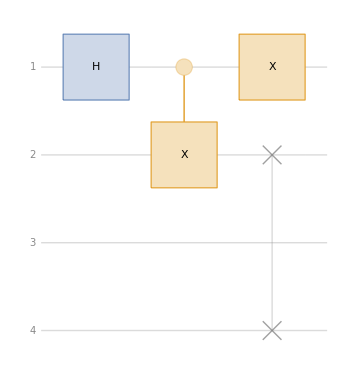

1/(√2)0001+1/(√2)1000

```mathematica
qs=(QuantumState["0000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["H",{1}],
	QuantumOperator["CX",{1,2}],
	QuantumOperator["X",{1}],
	QuantumOperator["SWAP",{4,2}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

0000

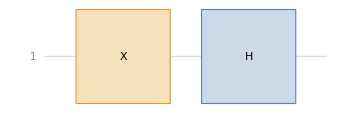

1/(√2)0000-1/(√2)1000

```mathematica
qs=(QuantumState["0000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["X",{1}],
	QuantumOperator["H",{1}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

0000

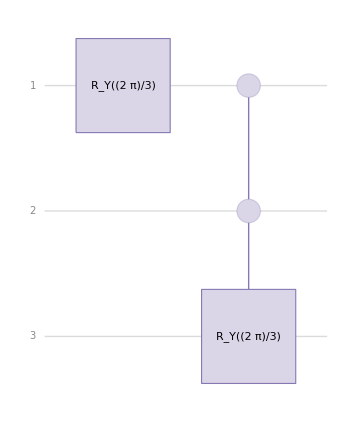

1/2 0000+(√3)/2 1000

```mathematica
qs=(QuantumState["0000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["RY"[2ArcCos[1/2]] ,{1}],
	QuantumOperator["Controlled"["RY"[2ArcCos[1/2]],{2,1}]]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

0000

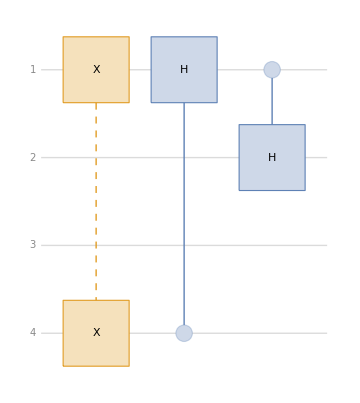

1/(√2)0001-1/21001-1/21101

```mathematica
qs=(QuantumState["0000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["X",{1,4}],
	QuantumOperator["CH",{4,1}],
	QuantumOperator["CH",{1,2}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

0000

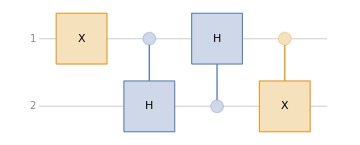

1/2 0100-1/21000+1/(√2)1100

```mathematica
qs=(QuantumState["0000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["X",{1}],
	QuantumOperator["CH",{1,2}],
	QuantumOperator["CH",{2,1}],
	QuantumOperator["CX",{1,2}]
	
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

0000

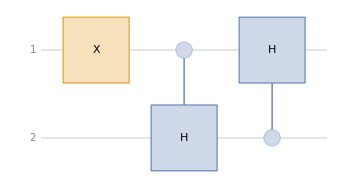

1/2 0100+1/(√2)1000-1/21100

```mathematica
qs=(QuantumState["0000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["X",{1}],
	QuantumOperator["CH",{1,2}],
	QuantumOperator["CH",{2,1}]
	
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

## The W state

http : // twoqubits . wikidot . com/ex5 - 11

0000

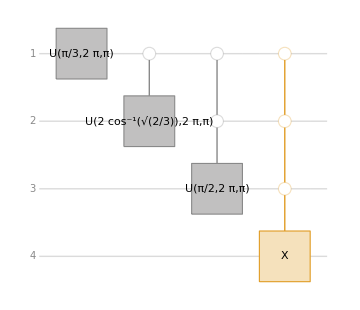

1/2 0001+1/2 0010+1/2 0100+1/2 1000

```mathematica
qs=(QuantumState["0000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator[{"U3",2π/6, 2π ,π},{1}],
	QuantumOperator[{"C0","U3"[2ArcCos[Sqrt[2/3]], 2π ,π]->{2},{1}}],
	QuantumOperator[{"C0","U3"[2(π/4), 2π ,π]->{3},{1,2}}],
	QuantumOperator[{"C0","X"->{4},{1,2,3}}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

```mathematica
maux[n_]:={{Sqrt[n-1]/Sqrt[n],1/Sqrt[n]},{1/Sqrt[n],-Sqrt[n-1]/Sqrt[n]}}
maux[n]//MatrixForm
maux[4]//MatrixForm
maux[3]//MatrixForm
maux[2]//MatrixForm
maux[1]//MatrixForm
```

((√(-1+n))/(√n) | 1/(√n)
1/(√n) | -(√(-1+n))/(√n))

((√3)/2 | 1/2
1/2 | -(√3)/2)

(√(2/3) | 1/(√3)
1/(√3) | -√(2/3))

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

(0 | 1
1 | 0)

```mathematica
Sqrt[3]/Sqrt[2]HadamardMatrix[2]//MatrixForm
```

((√3)/2 | (√3)/2
(√3)/2 | -(√3)/2)

```mathematica
maux[4]//MatrixForm
Solve[Cos[θ/2]==Sqrt[3]/2,θ]
Solve[1/2 Exp[I ϕ]==1/2,ϕ]
MatrixForm[QuantumOperator[{"U3",θ, ϕ ,λ}]["Matrix"]]
MatrixForm[QuantumOperator[{"U3",2π/6, ϕ ,λ}]["Matrix"]]
MatrixForm[(QuantumOperator[{"U3",2π/6, 2π ,π}])["Matrix"]]
```

((√3)/2 | 1/2
1/2 | -(√3)/2)

{{θ→ConditionalExpression[2 (-π/6+2 π C[1]), C[1]∈ℤ]},{θ→ConditionalExpression[2 (π/6+2 π C[1]), C[1]∈ℤ]}}

{{ϕ→ConditionalExpression[2 π C[1], C[1]∈ℤ]}}

(Cos[θ/2] | -ⅇ^(ⅈ λ) Sin[θ/2]
ⅇ^(ⅈ ϕ) Sin[θ/2] | ⅇ^(ⅈ (λ+ϕ)) Cos[θ/2])

((√3)/2 | -ⅇ^(ⅈ λ)/2
ⅇ^(ⅈ ϕ)/2 | 1/2 √3 ⅇ^(ⅈ (λ+ϕ)))

((√3)/2 | 1/2
1/2 | -(√3)/2)

```mathematica
maux[3]//MatrixForm
Solve[Cos[θ/2]==Sqrt[2/3],θ]
Solve[1/Sqrt[3] Exp[I ϕ]==1/Sqrt[3],ϕ]
MatrixForm[QuantumOperator[{"U3",θ, ϕ ,λ}]["Matrix"]]
MatrixForm[QuantumOperator[{"U3",2ArcCos[Sqrt[2/3]], ϕ ,λ}]["Matrix"]]
MatrixForm[(QuantumOperator[{"U3",2ArcCos[Sqrt[2/3]], 2π ,π}])["Matrix"]]
```

(√(2/3) | 1/(√3)
1/(√3) | -√(2/3))

{{θ→ConditionalExpression[2 (-ArcCos[√(2/3)]+2 π C[1]), C[1]∈ℤ]},{θ→ConditionalExpression[2 (ArcCos[√(2/3)]+2 π C[1]), C[1]∈ℤ]}}

{{ϕ→ConditionalExpression[2 π C[1], C[1]∈ℤ]}}

(Cos[θ/2] | -ⅇ^(ⅈ λ) Sin[θ/2]
ⅇ^(ⅈ ϕ) Sin[θ/2] | ⅇ^(ⅈ (λ+ϕ)) Cos[θ/2])

(√(2/3) | -ⅇ^(ⅈ λ)/(√3)
ⅇ^(ⅈ ϕ)/(√3) | √(2/3) ⅇ^(ⅈ (λ+ϕ)))

(√(2/3) | 1/(√3)
1/(√3) | -√(2/3))

```mathematica
maux[2]//MatrixForm
Solve[Cos[θ/2]==1/Sqrt[2],θ]
Solve[1/Sqrt[3] Exp[I ϕ]==1/Sqrt[3],ϕ]
MatrixForm[QuantumOperator[{"U3",θ, ϕ ,λ}]["Matrix"]]
MatrixForm[QuantumOperator[{"U3",2(π/4), ϕ ,λ}]["Matrix"]]
MatrixForm[(QuantumOperator[{"U3",2(π/4), 2π ,π}])["Matrix"]]
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

{{θ→ConditionalExpression[2 (-π/4+2 π C[1]), C[1]∈ℤ]},{θ→ConditionalExpression[2 (π/4+2 π C[1]), C[1]∈ℤ]}}

{{ϕ→ConditionalExpression[2 π C[1], C[1]∈ℤ]}}

(Cos[θ/2] | -ⅇ^(ⅈ λ) Sin[θ/2]
ⅇ^(ⅈ ϕ) Sin[θ/2] | ⅇ^(ⅈ (λ+ϕ)) Cos[θ/2])

(1/(√2) | -ⅇ^(ⅈ λ)/(√2)
ⅇ^(ⅈ ϕ)/(√2) | ⅇ^(ⅈ (λ+ϕ))/(√2))

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

## Hardy state

00

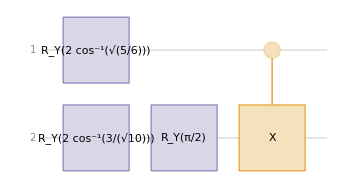

((√(3/2))/2-1/(2 √6))00+((√(3/2))/2+1/(2 √6))01+((√(3/10))/2+1/(2 √30))10+((√(3/10))/2-1/(2 √30))11

```mathematica
qs=(QuantumState["00"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["RY"[2ArcCos[Sqrt[5/6]]],{1}],
	QuantumOperator["RY"[2ArcCos[3/Sqrt[10]]],{2}],
	QuantumOperator["RY"[Pi/2],{2}],
	QuantumOperator["CX",{1,2}]
	
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

## Another Try

http://twoqubits.wikidot.com/ex5-12

00

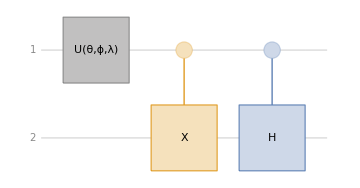

cos(θ/2)00+(ⅇ^(ⅈ ϕ) sin(θ/2))/(√2)10-(ⅇ^(ⅈ ϕ) sin(θ/2))/(√2)11

```mathematica
qs=(QuantumState["00"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["U3"[θ,ϕ,λ],{1}],
	QuantumOperator["CX",{1,2}],
	QuantumOperator["CH",{1,2}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

```mathematica
MatrixForm[QuantumOperator[{"U3",θ, ϕ ,λ}]["Matrix"]]
MatrixForm[QuantumOperator[{"U3",2ArcCos[Sqrt[5/6]], ϕ ,λ}]["Matrix"]]
MatrixForm[QuantumOperator[{"U3",2ArcCos[Sqrt[5/6]], 2π ,2π}]["Matrix"]]
```

(Cos[θ/2] | -ⅇ^(ⅈ λ) Sin[θ/2]
ⅇ^(ⅈ ϕ) Sin[θ/2] | ⅇ^(ⅈ (λ+ϕ)) Cos[θ/2])

(√(5/6) | -ⅇ^(ⅈ λ)/(√6)
ⅇ^(ⅈ ϕ)/(√6) | √(5/6) ⅇ^(ⅈ (λ+ϕ)))

(√(5/6) | -1/(√6)
1/(√6) | √(5/6))

```mathematica
Solve[Cos[θ/2]==Sqrt[10/12],θ]
Solve[1/Sqrt[6]Exp[I ϕ]==Sqrt[2/12],ϕ]
```

{{θ→ConditionalExpression[2 (-ArcCos[√(5/6)]+2 π C[1]), C[1]∈ℤ]},{θ→ConditionalExpression[2 (ArcCos[√(5/6)]+2 π C[1]), C[1]∈ℤ]}}

{{ϕ→ConditionalExpression[2 π C[1], C[1]∈ℤ]}}

```mathematica
λ==ϕ
```

λ==ϕ

00

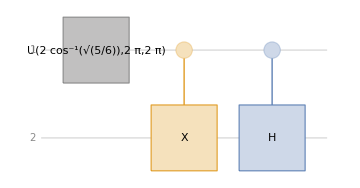

√(5/6)00+1/(2 √3)10-1/(2 √3)11

```mathematica
qs=(QuantumState["00"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator[{"U3",2ArcCos[Sqrt[5/6]], 2π ,2π},{1}],
	QuantumOperator["CX",{1,2}],
	QuantumOperator["CH",{1,2}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

```mathematica
MatrixForm[QuantumOperator[{"U3",θ, ϕ ,λ}]["Matrix"]]
MatrixForm[QuantumOperator[{"U3",2ArcCos[3/Sqrt[10]], ϕ ,λ}]["Matrix"]]
MatrixForm[QuantumOperator[{"U3",2ArcCos[3/Sqrt[10]], 2π ,2π}]["Matrix"]]
```

(Cos[θ/2] | -ⅇ^(ⅈ λ) Sin[θ/2]
ⅇ^(ⅈ ϕ) Sin[θ/2] | ⅇ^(ⅈ (λ+ϕ)) Cos[θ/2])

(3/(√10) | -ⅇ^(ⅈ λ)/(√10)
ⅇ^(ⅈ ϕ)/(√10) | (3 ⅇ^(ⅈ (λ+ϕ)))/(√10))

(3/(√10) | -1/(√10)
1/(√10) | 3/(√10))

```mathematica
Solve[Cos[θ/2]==3/Sqrt[10],θ]
Solve[1/Sqrt[10]Exp[I ϕ]==1/Sqrt[10],ϕ]
```

{{θ→ConditionalExpression[2 (-ArcCos[3/(√10)]+2 π C[1]), C[1]∈ℤ]},{θ→ConditionalExpression[2 (ArcCos[3/(√10)]+2 π C[1]), C[1]∈ℤ]}}

{{ϕ→ConditionalExpression[2 π C[1], C[1]∈ℤ]}}

Meaning of the Empty Dot in the V Gate
In your circuit diagram, the empty dot (open circle) on the control line of the V gate represents a 0-control (sometimes called a “controlled-on-zero” gate). This means the V gate (a single-qubit gate applied to the lower qubit) will be performed only when the control qubit (top wire) is in the state 
∣
0
⟩
∣0⟩.

Contrast:

A solid (filled) dot as on the H gate is a standard control (applies when the control is 
∣
1
⟩
∣1⟩).

An empty (open) dot is a 0-control (applies when the control is 
∣
0
⟩
∣0⟩).

Recap:
V Gate with Open Circle Control: V is applied if and only if the control qubit is in state 
∣
0
⟩
∣0⟩.

Circuit notation: Open circle = control on 
∣
0
⟩
∣0⟩, filled circle = control on 
∣
1
⟩
∣1⟩.

If you want to know the explicit effect, implementation, or the specific matrix for V or want to practice writing the logic for a 0-controlled gate, let me know!

00

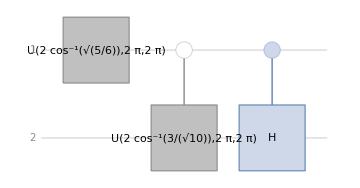

(√3)/2 00+1/(2 √3)01+1/(2 √3)10+1/(2 √3)11

```mathematica
qs=(QuantumState["00"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator[{"U3",2ArcCos[Sqrt[5/6]], 2π ,2π},{1}],
	QuantumOperator[{"C0","U3"[2ArcCos[3/Sqrt[10]], 2π ,2π]->{2},{1}}],
	QuantumOperator["CH",{1,2}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

```mathematica
3/Sqrt[12]
1/Sqrt[12]
```

(√3)/2

1/(2 √3)

## Question 5

000

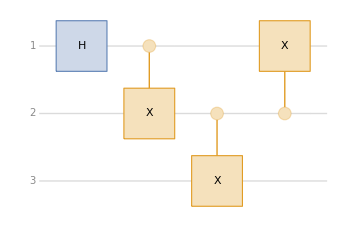

1/(√2)000+1/(√2)011

```mathematica
qs=(QuantumState["000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["H",{1}],
	QuantumOperator["CX",{1,2}],
	QuantumOperator["CX",{2,3}],
	QuantumOperator["CX",{2,1}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

000

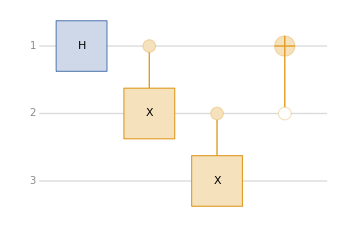

1/(√2)100+1/(√2)111

```mathematica
qs=(QuantumState["000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["H",{1}],
	QuantumOperator["CX",{1,2}],
	QuantumOperator["CX",{2,3}],
	QuantumOperator["C0NOT",{2,1}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

```mathematica
qs=(QuantumState["000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["H",{1}],
	QuantumOperator["CX",{1,2}],
	QuantumOperator["CX",{2,3}],
	QuantumOperator["CX",{2,1}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

000

-Graphics-

1/(√2)000+1/(√2)011

## Question 7

## A circuit that I saw in a paper

0000

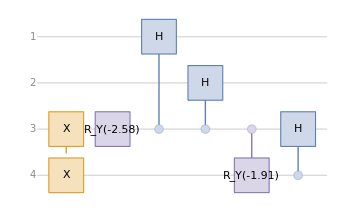

(0.736005+0. ⅈ)0001+(0.113109+0. ⅈ)0010+(0.622821+0. ⅈ)0011+(0.0565924+0. ⅈ)0101+(0.113109+0. ⅈ)0110+(-0.0565924+0. ⅈ)0111+(0.0565924+0. ⅈ)1001+(0.113109+0. ⅈ)1010+(-0.0565924+0. ⅈ)1011+(0.0565924+0. ⅈ)1101+(0.113109+0. ⅈ)1110+(-0.0565924+0. ⅈ)1111

0000

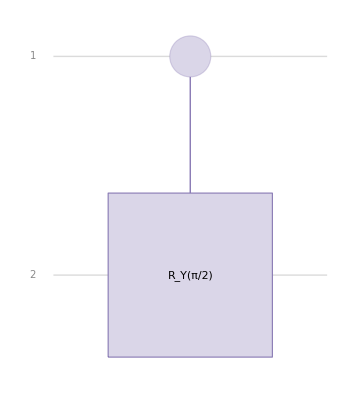

0000

```mathematica
qs=(QuantumState["0000"]);
TraditionalForm[qs]
qc=QuantumCircuitOperator[List[
	QuantumOperator["X",{3,4}],
	QuantumOperator["RY"[-2.58],{3}],
	QuantumOperator["CH",{3,1}],
	QuantumOperator["CH",{3,2}],
	QuantumOperator[{"C","RY"[-1.91]->{4},{3}}],
	QuantumOperator["CH",{4,3}]
]];
qc["Diagram"]
qc[qs]//TraditionalForm
```

```mathematica
qcH[θ1_,θ2_]:={{-Graphics-, QuantumCircuitOperator}}[{{{-Graphics-, QuantumOperator}}[{"YRotation",θ1}],{{-Graphics-, QuantumOperator}}[{"YRotation",θ2},{2}],{{-Graphics-, QuantumOperator}}["Toffoli"],{{-Graphics-, QuantumOperator}}[{"YRotation",π-θ1}],{{-Graphics-, QuantumOperator}}[{"YRotation",π-θ2},{2}]}];
```

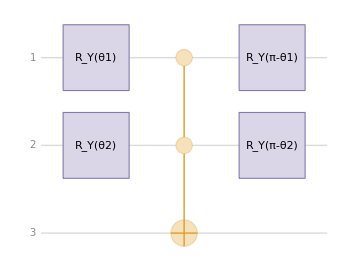

```mathematica
qcH[θ1,θ2]["Diagram"]
```

```mathematica
qs=(QuantumState["00"]);
qcH[2ArcCos[1/Sqrt[3]],2ArcSin[Sqrt[2/3]]][qs]//TraditionalForm
```

-2/9000+2/9 001+(2 √2)/9 010-(2 √2)/9011+(2 √2)/9 100-(2 √2)/9101+5/9 110+4/9 111